```mathematica
Clear["Global`*"];
```

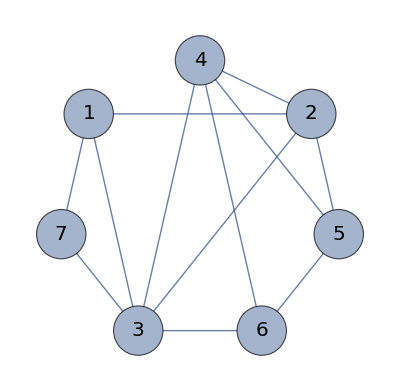

```mathematica
IndividualGraph = Graph[{1->7, 2->1,3->1,4->2,5->2,6->5,7->3, 2->3,3->6,4->3,4->5,4->6}, EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.05],VertexSize->Large,
VertexLabels->Placed["Name",Center], VertexLabelStyle->Directive[Black,Italic,20], GraphLayout->"CircularEmbedding"]
root = 2;
vertexCount = Length@VertexList@IndividualGraph;
```

```mathematica
pred = ConstantArray[0, vertexCount];
depth = ConstantArray[0, vertexCount];
thread = ConstantArray[0, vertexCount];
dinast = List[];
dir = ConstantArray[0, vertexCount];
```

Множество дуг покрывающего дерева:{2->4,4->3,3->7,7->1,3->6,6->5}

Множество дуг искходного графа без дуг покрывающего дерева:{2->1,2->3,3->1,4->5,4->6,5->2}

Покрывающее дерево с использованием Layout для деревьев

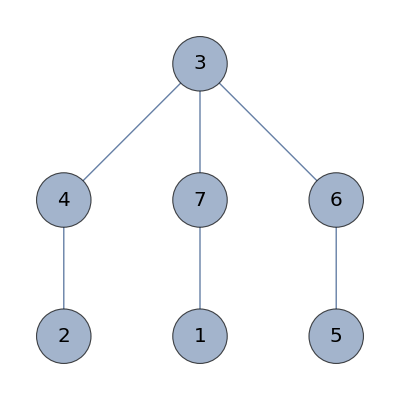

Покрывающее дерево с подсвеченным корнем

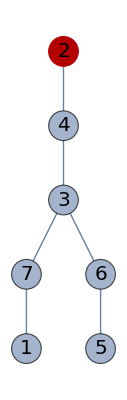

```mathematica
GetSpanningTree[graph_, root_]:=Module[
{resultTree = List[], count = 1},
DepthFirstScan[UndirectedGraph[graph],root, {"FrontierEdge"-> (({AppendTo[resultTree, DirectedEdge[First[#],Last[#]]],
pred[[Last[#]]]=First[#], depth[[Last[#]]]=depth[[First[#]]]+1})&),"PrevisitVertex"-> (( {If[!ContainsAny[dinast,{#}],AppendTo[dinast,
 #]],
thread[[#]]=count++})&)}];
Return@resultTree;
];
spanning = GetSpanningTree[IndividualGraph, root];
GetNotSpanningTreeEdges[graph_, spanningTreeEdges_]:=Module[
{result = List[], revercedSpanning, edges = EdgeList[graph]},
result = Complement[edges, spanningTreeEdges];
revercedSpanning = DirectedEdge[Last[#], First[#]]&/@spanningTreeEdges;
result = Complement[result, revercedSpanning];
Return@result;
]
notSpanningEdges = GetNotSpanningTreeEdges[IndividualGraph, spanning];
CellPrint[TextCell[Row[{"Множество дуг покрывающего дерева:", spanning}], "Output"]];
CellPrint[TextCell[Row[{"Множество дуг искходного графа без дуг покрывающего дерева:", notSpanningEdges}], "Output"]];
CellPrint[TextCell[Row[{"Покрывающее дерево с использованием Layout для деревьев"}], "Output"]];
spanningTreeGraph = Graph[spanning, GraphLayout->{"LayeredEmbedding"}, EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.05],VertexSize->Large,
VertexLabels->Placed["Name",Center], VertexLabelStyle->Directive[Black,Italic,20]]
CellPrint[TextCell[Row[{"Покрывающее дерево с подсвеченным корнем"}], "Output"]];
HighlightGraph[Graph[spanningTreeGraph, GraphLayout->{"LayeredEmbedding", "RootVertex"-> root}], root]
```

```mathematica
GetOrientedSpanningTree[graph_, spanningTree_]:=Module[
{result = List[], edges =EdgeList[graph]},
If[ContainsAny[edges, {#}],
AppendTo[result, #];
dir[[Last[#]]]=1,
AppendTo[result, DirectedEdge[Last[#],First[#]]];
dir[[Last[#]]]=-1]&/@spanningTree;
Return@result;
];
orientedSpanning = GetOrientedSpanningTree[IndividualGraph, spanning];
vertexStrings = ToString[#]&/@Sort@VertexList@IndividualGraph;
TableForm[{pred, depth, thread, dinast, dir}, TableAlignments-> Center, TableHeadings-> {{"pred", "depth", "thread","dinast", "dir"},vertexStrings}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7
pred | 7 | 0 | 4 | 2 | 6 | 3 | 3
depth | 4 | 0 | 2 | 1 | 4 | 3 | 3
thread | 5 | 1 | 3 | 2 | 7 | 6 | 4
dinast | 2 | 4 | 3 | 7 | 1 | 6 | 5
dir | -1 | 0 | 1 | -1 | 1 | 1 | -1

Исходный граф с подсвеченными дугами покрывающего дерева:

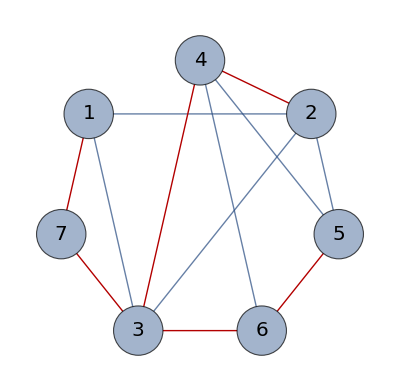

```mathematica
CellPrint[TextCell[Row[{"Исходный граф с подсвеченными дугами покрывающего дерева:"}],"Output"] ];
HighlightGraph[IndividualGraph, orientedSpanning]
```